```mathematica
t=AbsoluteTime[];result={};
threestatesreducedset=Table[Prime[n],{n,5000000}];
Do[If[IntegerQ[√(threestatesreducedset[[k]]-1)],AppendTo[result,threestatesreducedset[[k]]]],{k,Length[threestatesreducedset]}];
{AbsoluteTime[]-t,result}
```

{61.7293084,{2,5,17,37,101,197,257,401,577,677,1297,1601,2917,3137,4357,5477,7057,8101,8837,12101,13457,14401,15377,15877,16901,17957,21317,22501,24337,25601,28901,30977,32401,33857,41617,42437,44101,50177,52901,55697,57601,62501,65537,67601,69697,72901,78401,80657,90001,93637,98597,106277,115601,122501,147457,148997,156817,160001,164837,176401,184901,190097,193601,197137,215297,217157,220901,224677,240101,246017,287297,295937,309137,324901,331777,341057,352837,401957,404497,414737,417317,427717,454277,462401,470597,476101,484417,490001,495617,509797,512657,547601,562501,577601,583697,608401,614657,665857,682277,739601,746497,792101,820837,828101,846401,864901,876097,894917,902501,921601,933157,972197,1008017,1020101,1073297,1110917,1123601,1136357,1144901,1166401,1196837,1201217,1223237,1263377,1299601,1308737,1313317,1322501,1336337,1378277,1382977,1401857,1464101,1547537,1552517,1623077,1628177,1664101,1674437,1705637,1726597,1731857,1742401,1752977,1795601,1822501,1833317,1865957,1887877,1893377,1943237,1976837,1988101,2005057,2016401,2044901,2056357,2073601,2119937,2131601,2232037,2262017,2322577,2390117,2402501,2421137,2446097,2452357,2464901,2483777,2496401,2515397,2604997,2611457,2689601,2702737,2735717,2755601,2768897,2802277,2808977,2835857,2842597,2890001,2944657,3013697,3083537,3118757,3147077,3182657,3204101,3218437,3297857,3326977,3422501,3459601,3496901,3519377,3549457,3587237,3648101,3686401,3763601,3857297,3865157,3880901,3896677,3920401,3960101,4024037,4104677,4137157,4202501,4218917,4227137,4260097,4301477,4326401,4343057,4351397,4384837,4393217,4435237,4477457,4494401,4519877,4562497,4639717,4726277,4884101,4946177,5107601,5134757,5225797,5262437,5308417,5336101,5354597,5382401,5410277,5428901,5456897,5541317,5569601,5664401,5779217,5788837,5856401,5904901,6022117,6031937,6051601,6071297,6100901,6230017,6330257,6421157,6431297,6502501,6604901,6635777,6728837,6760001,6780817,6885377,7001317,7043717,7096897,7107557,7160977,7203857,7290001,7322437,7452901,7485697,7540517,7584517,7617601,7650757,7672901,7706177,7728401,7806437,7862417,7974977,8031557,8042897,8122501,8202497,8271377,8317457,8352101,8386817,8410001,8503057,8549777,8561477,8608357,8667137,8761601,8785297,8844677,8916197,9096257,9156677,9278117,9326917,9449477,9572837,9647237,9672101,9821957,9834497,9859601,9960337,9985601,10074277,10137857,10214417,10265617,10329797,10368401,10497601,10536517,10588517,10666757,10719077,10758401,10824101,10916417,10929637,10982597,11062277,11115557,11155601,11222501,11262737,11289601,11383877,11492101,11806097,11874917,12068677,12110401,12180101,12278017,12362257,12390401,12460901,12489157,12503297,13133377,13278737,13322501,13395601,13468901,13586597,13808657,13912901,13942757,14032517,14092517,14107537,14167697,14243077,14258177,14318657,14364101,14394437,14440001,14485637,14638277,14822501,14976901,15085457,15132101,15163237,15210001,15288101,15397777,15570917,15729157,15872257,15952037,16048037,16192577,16208677,16273157,16370117,16451137,16564901,16646401,16695397,16924997,16974401,17007377,17106497,17139601,17189317,17255717,17272337,17388901,17422277,17438977,17472401,17505857,17690437,17859077,18062501,18147601,18198757,18438437,18490001,18576101,18748901,18800897,18835601,19044497,19061957,19096901,19131877,19219457,19395217,19448101,19483397,19749137,19855937,20016677,20124197,20214017,20286017,20340101,20466577,20520901,20557157,20611601,20738917,20848357,21068101,21160001,21196817,21215237,21288997,21307457,21566737,21622501,21771557,22090001,22127617,22240657,22335077,22410757,22429697,22600517,22848401,22886657,22905797,22982437,23001617,23367557,23522501,23775377,23872997,23951237,24049217,24108101,24206401,24364097,24443137,24542117,24561937,24900101,25040017,25140197,25160257,25300901,25441937,25542917,25563137,25765777,25806401,25867397,26214401,26275877,26563717,26728901,26790977,26832401,26977637,27040001,27081617,27311077,27415697,27520517,27604517,27625537,27709697,28026437,28132417,28238597,28515601,28558337,28729601,28836901,28987457,29203217,29376401,29419777,29484901,29658917,29877157,29964677,29986577,30096197,30140101,30250001,30316037,30360101,30514577,30647297,30802501,30913601,30958097,30980357,31069477,31181057,31203397,31248101,31584401,31990337,32080897,32490001,32604101,32764177,32787077,32878757,33131537,33177601,33339077,33686417,33802597,33918977,33988901,34035557,34222501,34292737,34409957,34503877,34527377,34574401,35164901,35331137,35521601,35569297,35640901,35808257,35880101,35952017,36072037,36120101,36192257,36360901,36554117,36723601,37161217,37332101,37454401,37527877,37576901,37625957,37699601,37896337,37994897,38019557,38142977,38316101,38638657,38688401,38862757,38887697,38937601,39112517,39262757,39765637,39866597,40195601,40322501,40449601,40525957,40960001,41216401,41396357,41731601,41990401,42432197,42640901,42719297,42771601,42850117,42902501,43243777,43428101,43612817,43744997,44036497,44169317,44943617,45024101,45077797,45212177,45346757,45751697,45914177,45968401,46022657,46049797,46240001,46321637,46566977,46594277,46922501,46977317,47141957,47251877,47389457,47748101,47969477,48024901,48219137,48385937,48580901,48720401,48776257,48860101,48944017,49140101,49196197,49224257,49617937,49702501,49928357,50410001,50608997,50836901,51122501,51265601,51322897,51696101,52070657,52417601,52475537,52707601,53085797,53348417,53523857,53670277,54228497,54523457,54819217,54908101,54967397,55056401,55264357,55591937,55651601,55741157,55860677,56100101,56310017,56490257,56550401,56610577,56791297,57002501,57699217,57820817,58125377,58614337,58890277,59536657,59598401,59814757,59969537,60124517,60372901,60435077,60528401,60777617,60902417,60933637,60996101,61152401,61402897,61685317,61716737,61842497,62504837,62568101,63107137,63138917,63297937,64224197,64480901,64545157,65028097,65286401,65610001,65836997,65869457,66814277,66846977,66912401,66977857,67141637,67174417,67338437,67404101,67667077,67732901,68128517,68392901,68724101,68823617,68956417,69288977,69722501,70157377,70324997,70896401,70963777,71132357,71470117,72250001,72931601,73102501,73170917,73547777,73685057,74132101,74407877,74545957,74926337,75168901,75342401,75411857,75585637,75794437,76038401,76562501,76737601,76983077,77158657,77193797,77264101,77721857,78251717,78393317,78783377,78854401,79103237,79923601,80353297,80532677,80568577,80928017,81000001,81180101,81288257,81360401,81432577,81830117,81974917,83174401,83247377,83283877,83795717,83978897,84272401,84713617,84897797,85377601,85488517,85747601,85858757,85932901}}

```mathematica
issue={};Do[{t=AbsoluteTime[];result={};
threestatesreducedset=Table[Prime[n],{n,nb}];
Do[If[IntegerQ[√(threestatesreducedset[[k]]-1)],AppendTo[result,threestatesreducedset[[k]]]],{k,Length[threestatesreducedset]}];
AppendTo[issue,{nb,AbsoluteTime[]-t}]},{nb,100000,1000000,100000}]
```

```mathematica
issue
```

{{100000,1.029602},{200000,2.168404},{300000,3.338406},{400000,4.539608},{500000,5.7408101},{600000,6.9420122},{700000,8.1276143},{800000,9.3600164},{900000,10.592419},{1000000,11.824821}}

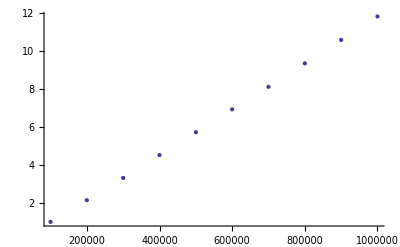

```mathematica
ListPlot[issue]
```

```mathematica
100000(#[[2]])/(#[[1]])&/@issue
```

{1.029602,1.084202,1.112802,1.134902,1.148162,1.157002,1.1610878,1.170002,1.1769354,1.1824821}

```mathematica
100000(#[[2]])/(#[[1]] Log[#[[1]]]^(2/3))&/@issue
```

{0.2019353,0.2045155,0.2053868,0.20633967,0.20637724,0.20606191,0.20520757,0.20542654,0.20545868,0.20537612}

```mathematica
NSolve[{nb1(1+nb1)/2==(nb1+nb2+1)/2(nb2-nb1)==(nb2+nb3+1)/2(nb3-nb2)==(nb3+nb4+1)/2(nb4-nb3),nb4==5000000},{nb1,nb2,nb3,nb4}][[6]]
```

{nb1→2.5×10^6,nb2→3.53553×10^6,nb3→4.33013×10^6,nb4→5.×10^6}

```mathematica
Clear[nb4]
```